```mathematica
Clear[Lx,Ly,A,
sx3d,SX3D,sx3dp,SX3DP,
sy3d,SY3D,sy3dp,SY3DP,
sz3d,SZ3D,sz3dp,SZ3DP,
cx3d,CX3D,cx3dp,CX3DP,
cy3d,CY3D,cy3dp,CY3DP,
cz3d,CZ3D,cz3dp,CZ3DP,
cons,Cons]
```

```mathematica
Lx=10;
Ly=10;
Lz =10;
A=Lx*Ly*Lz;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sx3d[j+k Lx+l Lx Ly,j+1+k Lx + l Lx Ly]=-I/2,sx3d[j+1+k Lx + l Lx Ly,j+k Lx+l Lx Ly]=I/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

SX3D=Table[sx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx3dp[i_Integer,j_Integer]=0;

Do[Do[{sx3dp[(k+1)Lx+ l Lx Ly,1+k Lx+ l Lx Ly]=-I/2,sx3dp[1+k Lx+ l Lx Ly,(k+1)Lx+ l Lx Ly]=I/2},{k,0,Ly-1}],{l,0,Lz-1}]

SX3DP=Table[sx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=-I/2,sy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

SY3D=Table[sy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy3dp[i_Integer,j_Integer]=0;

Do[Do[{sy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=-I/2,sy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{l,0,Lz-1}]

SY3DP=Table[sy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cx3d[j+k Lx+l Lx Ly,j+1+k Lx+l Lx Ly]=1/2,cx3d[j+1+k Lx+l Lx Ly,j+k Lx+l Lx Ly]=1/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

CX3D=Table[cx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx3dp[i_Integer,j_Integer]=0;

Do[Do[{cx3dp[(1+k)Lx+l Lx Ly,1+k Lx+l Lx Ly]=1/2,cx3dp[1+k Lx+l Lx Ly,(1+k)Lx+l Lx Ly]=1/2},{k,0,Ly-1}],{l,0,Lz-1}]

CX3DP=Table[cx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=1/2,cy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

CY3D=Table[cy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy3dp[i_Integer,j_Integer]=0;

Do[Do[{cy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=1/2,cy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{l,0,Lz-1}]

CY3DP=Table[cy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cz3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cz3d[j+(k-1) Lx+(l-1) Lx Ly,j+(k-1)Lx+l Lx Ly]=1/2,cz3d[j+(k-1)Lx+l Lx Ly,j+(k-1) Lx+(l-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}],{l,1,Lz-1}]

CZ3D=Table[cz3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cz3dp[i_Integer,j_Integer]=0;

Do[Do[{cz3dp[(k-1)Lx+j+(Lz-1) Lx Ly,(k-1)Lx+j]=1/2,cz3dp[(k-1)Lx+j,(k-1)Lx+j+(Lz-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}]

CZ3DP=Table[cz3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0;

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[CX3Doctave,CY3Doctave,CZ3Doctave,CX3Dpoctave,CY3Dpoctave,CZ3Dpoctave,
SX3Doctave,SY3Doctave,SZ3Doctave,SX3Dpoctave,SY3Dpoctave,SZ3Dpoctave]
```

```mathematica
CX3Doctave = Import["cx3d.dat"];
CY3Doctave = Import["cy3d.dat"];
CZ3Doctave = Import["cz3d.dat"];
CX3Dpoctave = Import["cx3dp.dat"];
CY3Dpoctave = Import["cy3dp.dat"];
CZ3Dpoctave = Import["cz3dp.dat"];

SX3Doctave =I* Import["sx3d.dat"];
SY3Doctave = I*Import["sy3d.dat"];
SZ3Doctave = I*Import["sz3d.dat"];
SX3Dpoctave =I*Import["sx3dp.dat"];
SY3Dpoctave = I*Import["sy3dp.dat"];
SZ3Dpoctave = I*Import["sz3dp.dat"];
```

Max[Abs[CX3D - CX3Doctave]]

Max[Abs[CY3D - CY3Doctave]]

Max[Abs[CZ3D - CZ3Doctave]]

Max[Abs[CX3DP - CX3Dpoctave]]

Max[Abs[CY3DP - CY3Dpoctave]]

Max[Abs[CZ3DP - CZ3Dpoctave]]

Max[Abs[SX3D - SX3Doctave]]

Max[Abs[SY3D - SY3Doctave]]

Max[Abs[SZ3D - SZ3Doctave]];

Max[Abs[SX3DP - SX3Dpoctave]]

Max[Abs[SY3DP - SY3Dpoctave]]

Max[Abs[SZ3DP - SZ3Dpoctave]];

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,αx_,αy_,αz_]:=t*(KroneckerProduct[SX3D+αx*SX3DP,σ1]+KroneckerProduct[SY3D+αy*SY3DP, σ2])+KroneckerProduct[2*Cons-t0*(CX3D+CY3D+αx*CX3DP+αy*CY3DP),σ3]+KroneckerProduct[tz *(CZ3D + αz*CZ3DP)-m*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM[1.,1.,0,1,0,0,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{Re[val],vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

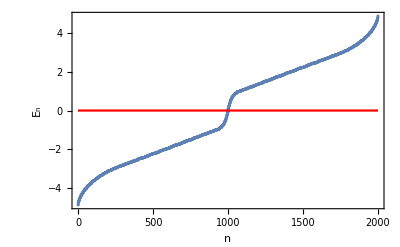

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

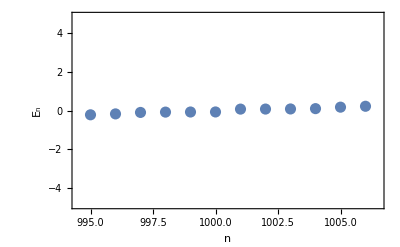

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}},PlotStyle->{PointSize[0.02]}],(**Plot[0,{x,0,2A},PlotStyle-> Red],**)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"},PlotRange->{{A+0.5-6,A+0.5+6},Automatic}]
```

```mathematica
ValVecAHI[[A]][[1]]
```

-0.0738232

```mathematica
Clear[a,b]
```

```mathematica
b=ValVecAHI[[A]][[2]];
```

```mathematica
Energy = ValVecAHI[[A]][[1]]
```

-0.0738232

```mathematica
(** a = Abs[b]*Abs[b]; **)
```

```mathematica
a=Sum[Abs[ValVecAHI[[A-l]][[2]]]*Abs[ValVecAHI[[A-l]][[2]]],{l,0,0}];
```

```mathematica
DensityVector = {};Do[Do[Do[DensityVector=Append[DensityVector,{i,j,k,a[[2(i + (j-1)*Lx + (k-1)*Lx * Ly)]]+a[[2(i + (j-1)*Lx + (k-1)*Lx * Ly)-1]]}],{i,1,Lx}],{j,1,Ly}],{k,1,Lz}]
```

```mathematica
Clear[datDiracIns,colorfunc,rng,P1]
```

```mathematica
datDiracIns=DensityVector;
```

```mathematica
datDiracIns;
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
(** colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]; **)
```

```mathematica
rng={0,Max[#]}&@datDiracIns[[All,4]];
```

```mathematica
rng[[2]]
```

0.00914989

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.02"},{rng[[2]]-10^-4,"0.04"}}]
```

```mathematica
Graphics3D[{PointSize[0.020],colorfunc[#[[4]],rng[[2]]],Point[#[[1;;3]]]}&/@datDiracIns,Axes->True,BoxRatios->1,BoxStyle->Directive[Thickness[0.0075]],AxesLabel->{"x","y","z"},BaseStyle->15,Ticks-> {{{1,"1"},{8,"8"}},{{1,"1"},{8,"8"}},{{1,"1"},{8,"8"}}},PlotRange->{{1,Lx},{1,Ly},{1,Lz}},ImageSize->400]
```

-Graphics3D-